## Computing runtime ratios for dyadic frame vs. stabiliser rank simulators for many magic state copies (Figure 6.11 in “Advancing classical simulators by measuring the magic of quantum computation”, James R. Seddon (2021))

```mathematica
TauRatio[d_,m_,Λ_]:=Λ^m d^3
```

t copies of T resource state

```mathematica
L0 = 1.1716
```

1.1716

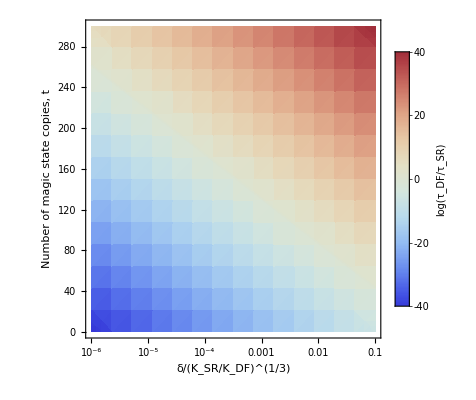

```mathematica
p1 = DensityPlot[Log[TauRatio[d,m,L0]], {d,10^-6,10^-1}, {m,0,300}, PlotLegends->BarLegend[Automatic,LegendLabel->"log(τ_DF/τ_SR)"], ScalingFunctions->{"Log",None},ColorFunction->(ColorData["ThermometerColors"][Rescale[#,{-45,45}]]&), MeshFunctions->{#3&},Mesh->{{0}}, MeshStyle->{GrayLevel[0.6],Thick},PlotRange->{Full,Full,{-45,45}},ColorFunctionScaling->False,LabelStyle->{FontSize->18, FontFamily->"Arial",GrayLevel[0.3]},FrameLabel->{"δ/(K_SR/K_DF)^(1/3)","Number of magic state copies, t" },ImageSize->{400,400}]
```

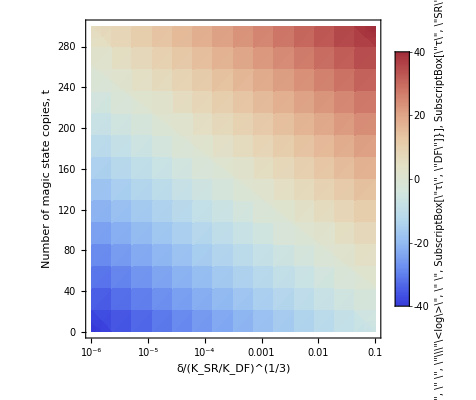

t copies of pi/64 state

```mathematica
L1 = 1.0386
```

1.0386

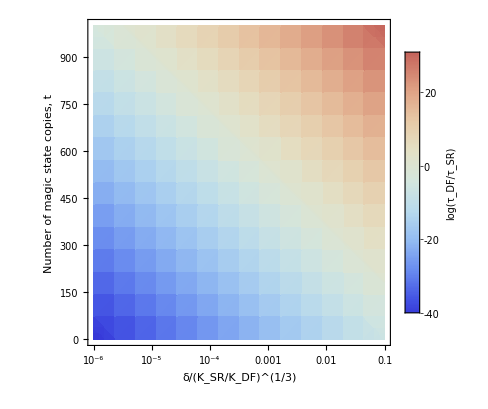

```mathematica
p2 = DensityPlot[Log[TauRatio[d,m,L1]], {d,10^-6,10^-1}, {m,0,1000}, PlotLegends->BarLegend[Automatic,LegendLabel->"log(τ_DF/τ_SR)"], ScalingFunctions->{"Log",None},ColorFunction->(ColorData["ThermometerColors"][Rescale[#,{-45,45}]]&), MeshFunctions->{#3&},Mesh->{{0}}, MeshStyle->{GrayLevel[0.6],Thick},PlotRange->{Full,Full,{-45,45}},ColorFunctionScaling->False,LabelStyle->{FontSize->18, FontFamily->"Arial",GrayLevel[0.3]},FrameLabel->{"δ/(K_SR/K_DF)^(1/3)","Number of magic state copies, t" },ImageSize->{410,410}]
```